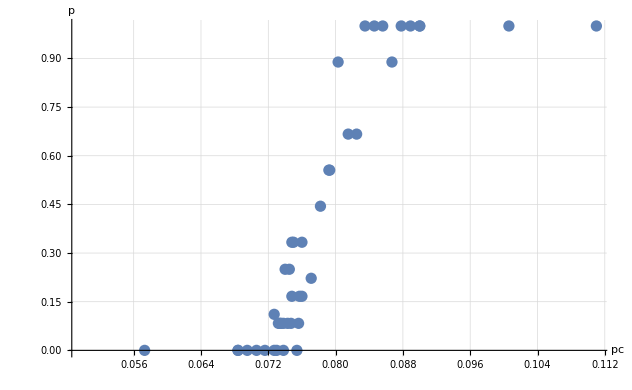

```mathematica
vec = Import["/home/syx/SYXrepo/vacation_homework/percolation/img/data.txt","Data"];

fig = ListPlot[vec,AxesLabel->{"pc","p"},PlotTheme->"Grid",PlotStyle-> Thick]
```

```mathematica
Export["/home/syx/SYXrepo/vacation_homework/percolation/texfile/fig1.jpg",fig,"JPEG",ImageResolution->500]
Import[%]
```